# Kapitola 7 - Pokrytí dat jednoduchou RBF sítí Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují dva dobře oddělené shluky, každý shluk reprezentuje jednu třídu.
Vygenerujeme tyto dva shluky dat.

```mathematica
values=50;
cluster1 =RandomReal[{-2,1},{values,2}];
cluster2=RandomReal[ {9,12},{values,2}];
inData = Join[cluster1,cluster2];
outcluster1=ConstantArray[{1,0},{values}];
outcluster2 = ConstantArray[{0,1},{values}];
outData= Join[outcluster1,outcluster2];
```

Takto vypadají naše vynerovaná vstupní data. Data můžeme chápat jako seznam bodů, určených svými {x,y} souřadnicemi.

```mathematica
inData
```

{{0.946367,-0.743795},{-1.54355,0.397125},{-1.56598,-0.424},{0.543026,0.566336},{-1.27661,-1.72296},{-0.404642,-1.68199},{-0.916299,-0.697098},{0.118573,0.274278},{-0.140093,-0.506505},{0.332489,-0.499936},{0.577345,0.918229},{-0.901718,0.125276},{-1.06163,0.0510666},{-1.89847,-1.51322},{-1.8601,-1.72407},{0.520986,-0.444187},{0.113391,-1.18095},{-0.34694,0.910063},{-0.397628,-1.62487},{-1.29114,-0.58083},{-0.844111,-1.86077},{-1.23224,-1.1101},{-1.39426,0.739132},{-0.370034,-1.32178},{-1.57417,-0.63787},{-0.52727,0.659901},{-0.465695,-1.45213},{-1.46031,-0.856324},{-1.23059,-0.259541},{-0.361086,0.286575},{0.736786,-0.817346},{-1.01222,-0.766879},{-0.120182,0.70685},{-1.64309,0.664397},{-1.55599,0.0394683},{-1.52041,0.129107},{-1.75054,-1.65675},{0.306084,-1.82006},{0.709324,-0.563461},{-1.92153,-0.460837},{0.35462,-0.638049},{0.751622,-1.41077},{0.435172,0.48264},{0.89674,-1.43441},{0.163166,-0.341679},{0.123163,-0.574436},{-0.402095,0.995171},{-1.62176,-1.78111},{0.64696,-1.95132},{0.421145,-1.246},{9.69852,9.12804},{10.0706,9.63153},{9.31653,11.6666},{10.3074,10.0073},{10.292,11.3686},{11.2216,10.8598},{11.6794,9.45072},{10.3407,10.8353},{10.2246,11.7571},{9.91821,11.8862},{9.14112,10.9224},{10.4553,11.611},{10.7214,9.09001},{9.86408,10.7228},{9.96623,11.0105},{10.5575,10.3085},{10.8386,9.96244},{9.38336,11.7181},{9.02253,11.4667},{11.9355,10.8901},{11.952,10.2591},{9.56389,11.8998},{10.2892,9.64916},{10.703,9.31453},{10.5932,10.6123},{11.1879,11.0138},{11.7905,10.8209},{10.6653,11.9837},{11.4395,11.2728},{9.50001,11.9299},{9.81435,10.7616},{9.88596,11.4912},{10.6975,10.5551},{11.3739,11.1536},{10.7879,11.3409},{11.5486,11.7716},{9.66935,9.94995},{10.7343,11.2596},{9.76169,10.4302},{10.8585,9.83565},{9.84611,9.46014},{10.659,11.8771},{9.77038,9.84417},{10.0047,10.6482},{10.7012,9.86489},{11.7728,10.0026},{10.5742,10.437},{11.074,10.1165},{10.5306,9.3422},{11.8423,11.3902}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat je reprezentována jinou barvou.

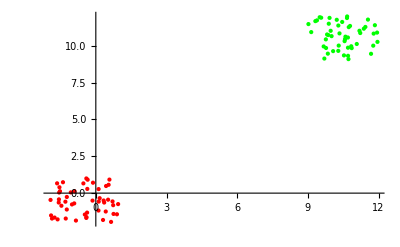

```mathematica
ListPlot[{cluster1,cluster2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1, OutputNonlinearity->Sigmoid,LinearPart->False,RandomInitialization->True]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 23, 0, 7, 56.9198367}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-5-23 at 0:07. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

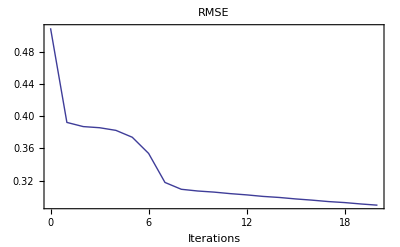

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Podívejme se jak naše síť klasifikuje data.

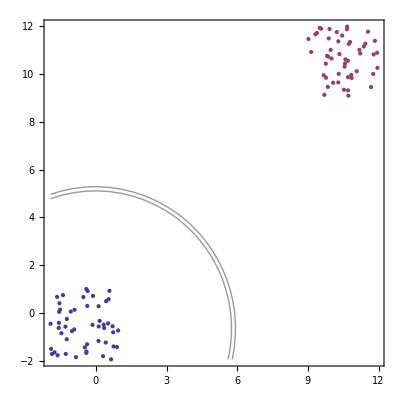

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronu

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Pro získání výstupu RBF neuronu je třeba upravit strukturu sítě. RBF neuron napojíme přímo na výstupní neuron s vahou 1. Na tomto výstupním neuronu uvidíme přímo výstup RBF neuronu. Následujísí obrázek zobrazuje síť před provedenými úpravami.

Následující obrázek ukazuje síť po provedené úpravě. Síť má pouze jeden výstup protože máme pouze jeden RBF neuron.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[1],{0}];(*změna matice vah na výstupu*)
```

A zobrazíme výstup RBF neuronu.

```mathematica
gauss=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data pro lepší představu o jejich pokrytí.

```mathematica
cluster13d=cluster1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
cluster23d=cluster2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
gaussO=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All,PlotStyle->Opacity[0.5]];
data3d=ListPointPlot3D[{cluster13d,cluster23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gaussO,data3d]
```

-Graphics3D-

## Prohlášení

Tento text je vypracován jako součást bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.